# Physics 230 -- Lab 11 (Complex Analysis)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 R. Steven Turley, BYU Physics & Astronomy, Fall 2011

Complex numbers are essential to the mathematical analysis of physical systems.  Because the field of complex numbers is algebraically closed while the field of real numbers is not, we can't help running into them from time to time.  Loosely speaking, "algebraically closed" essentially means that real polynomial equations will always have complex solutions when no real solutions exist.  In this lab, we will explore the behavior of several well-known functions in the complex plane and their application to oscillatory phenomena.

## Complex algebra (35 min)

### (#1) Complex numbers (10 min)

Mathematica uses a capital "I" to represent the imaginary number √-1in standard input.  In descriptive cells like this one, however, we will follow standard conventions by using a lower-case italicized "i ".  

(a) In the cell below, we define the complex number, zzz = 1 + i , and calcluate its real part (Re), imaginary part (Im), absolute value (Abs), phase in radians (Arg), normalized value (Sign) and complex conjugate (Conjugate).  Make sure that you understand the output, and then explain it to your TA.

```mathematica
zzz=1+I
Re[zzz]
Im[zzz]
Abs[zzz]
Arg[zzz]
Sign[zzz]
Conjugate[zzz]
```

1+ⅈ

1

1

√2

π/4

(1+ⅈ)/(√2)

1-ⅈ

(b)  Because z = x + i y  is a number in the complex plane, it can also be represented as a point {x, y} in the traditional xy plane.  With this analogy in hand, we often use the traditional xy plane to represent the complex plane, and refer to the x and y axes as the real and imaginary axes, respectively.  In the cell below, create a function comp2pair[z_] that converts a complex number z into the corresponding {x, y} point, and demonstrate its use.

```mathematica
comp2pair[z_]:=Module[{x,y},
x = Re[z];
y = Im[z];
{x,y}
]
comp2pair[zzz]
```

{1,1}

(c) Use RandomComplex to generate 100 random complex numbers within the rectangle defined by corners at -1-i  and 1+i .  Use your comp2pair function above to convert them to xy points and ListPlot them using AspectRatio → 1.

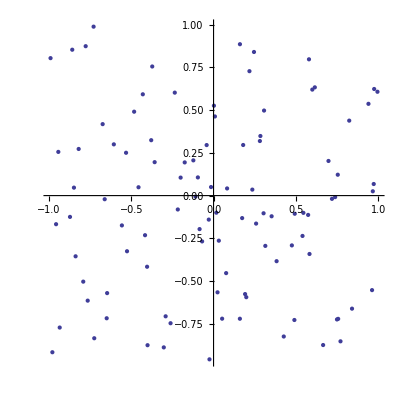

```mathematica
zz = RandomComplex[{-1-I,1+I},100];
xy = comp2pair[#]&/@zz;
ListPlot[xy,AspectRatio->1]
```

### (#2) Euler formula (10 min)

(a) Use TrigToExp to convert hyperbolic trig functions cosh(x) and sinh(x) into exponential form.  These should look familiar.  Then use ExpToTrig to bring them back to trigonometric form.

```mathematica
exp = TrigToExp[Cosh[x]]
exp2 =TrigToExp[Sinh[x]]
ExpToTrig[exp]
ExpToTrig[exp2]
```

ⅇ^-x/2+ⅇ^x/2

-ⅇ^-x/2+ⅇ^x/2

Cosh[x]

Sinh[x]

(b) Use ExpToTrig to convert exponential function ⅇ^x into trigonometric form.

```mathematica
ExpToTrig[Exp[x]]
```

Cosh[x]+Sinh[x]

(c) Use ExpToTrig to convert the exponential function ⅇ^(i x) into trigonometric form.  This identity, often called Euler's formula, provides a geometric link between the complex plane and the unit circle.  Euler's formula is the most important concept that you will encounter in this lab -- commit it to memory if you haven't already done so.

```mathematica
ExpToTrig[Exp[I*x]]
```

Cos[x]+ⅈ Sin[x]

(d) Use TrigToExp to convert sin(x) and cos(x) into exponential form.  You should also commit these identities to memory.

```mathematica
TrigToExp[Sin[x]]
TrigToExp[Cos[x]]
```

1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)

ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2

### (#3) The unit circle (5 min)

In the sciences, we will often use ⅇ^(i ω t) to represent a time-oscillating quantity, though it is implicitly understood that only the real part of the expression is physical.  The expression ⅇ^(i θ) is often referred to as a complex sinusoid.  

Evaluate the cell below, which animates the arrow pointing towards z = ⅇ^(i θ) in the complex plane as θ is varied between 0 and 2π.  The real and imaginary components of z are also animated as large red and blue dots, respectively.  Explain the various features of the graphic to your TA.

```mathematica
g[th_] :=Exp[I  th]

objects[th_] := {Circle[],Arrowheads[0.1],Thick,Arrow[{{0,0},{Cos[th],Sin[th]}}], PointSize[0.05],Red,Point[{Cos[th],0}], Blue,Point[{0,Sin[th]}]}

Manipulate[ Graphics[objects[t] ,Axes->True,AxesLabel->{"x","y"}],{t,0,2Pi}]
```

### (#4) Complex algebra (5 min)

(a)  Euler's formula makes it possible to express any complex number in terms of a magnitude and a phase.  Use Exp, Abs and Arg to define a function convexp[z_] that converts a complex number z into exponential form.  Try your new function to show that 1+i  = √2 ⅇ^((ⅈ π)/4).

```mathematica
convexp[z_]:=Module[{r,θ},
r = Abs[z];
θ = Arg[z];
r*Exp[I*θ]
]
convexp[1+I]
```

√2 ⅇ^((ⅈ π)/4)

(b) In the cell below, we use the exponential form to define two complex numbers, z_1 and z_2.  Evaluate the cell to see how their magnitudes and phases combine under multiplication and division.  Explain the output to your TA.  Observe that ComplexExpand separates a complex expression into overall real and imaginary parts by assuming that all of the variables in the expression are real numbers.  This is a very useful trick -- remember it.

```mathematica
z1 = Subscript[r, 1]*Exp[I Subscript[ϕ, 1]]; z2 = Subscript[r, 2]*Exp[I Subscript[ϕ, 2]];

z1*z2//Simplify
z1*z2//ComplexExpand

z1/z2//Simplify
z1/z2//ComplexExpand
```

ⅇ^(ⅈ (ϕ_1+ϕ_2)) r_1 r_2

Cos[ϕ_1+ϕ_2] r_1 r_2+ⅈ Sin[ϕ_1+ϕ_2] r_1 r_2

(ⅇ^(ⅈ (ϕ_1-ϕ_2)) r_1)/r_2

(Cos[ϕ_1-ϕ_2] r_1)/r_2+(ⅈ Sin[ϕ_1-ϕ_2] r_1)/r_2

### (#5) Complex roots (5 min)

(a) In the cell below, we use Solve to find the two square roots of -1.  Modify the equation to find the 3 cube roots of i.  Then manually cube each root to make sure you get i  back again.

```mathematica
root = z/.Solve[z^3==-1,z]//ComplexExpand
root[[1]]^3
root[[2]]^3//Simplify
root[[3]]^3//Simplify
```

{-1,1/2+(ⅈ √3)/2,1/2-(ⅈ √3)/2}

-1

-1

-1

(b) Evaluate the cell below in order to define circleroots[n_], a function that graphically and dynamically illustrates the n^throots of complex numbers that lie on the unit circle.  The example provided allows you to visualize the square roots (i.e. n = 2) of unit-circle points.  Use your mouse to continuously vary the sample point.  After interactively exploring several different n values, demonstrate and explain one interesting case in detail for your TA.

```mathematica
circleroots[rootnum_] :=DynamicModule[{p={1,0},zz,pair2comp,comp2pair,makeroots,setpoint,arrows,objects,options},
pair2comp[{x_,y_}] := x + I y;
comp2pair[z_] := {Re[z],Im[z]};
makeroots[z_,n_] := (zz/.Solve[zz^n==z,zz]);
setpoint = Dynamic@{Arrow[{{0,0},Normalize[p]}],PointSize[0.025],Black,Point[Normalize[p]]};
arrows = Dynamic[Arrow[{{0,0},#}]&/@ comp2pair/@ makeroots[pair2comp[Normalize[p]],rootnum]];
objects = Dynamic@{Circle[],Arrowheads[0.1],Thick,Blue,arrows,Red,setpoint};
options = {PlotRange->1.1{{-1,1},{-1,1}},PlotLabel->Dynamic[Magnify[pair2comp[Normalize[p]],2]],Axes->True,AxesLabel->{"x(real)","y(imag)"},LabelStyle->Medium};
LocatorPane[Dynamic[p],Graphics[objects,options],Appearance->None]
]

circleroots[150]
```

## Complex Functions (40 min)

### (#6) Functions in the complex plane I (15 min)

(a) Plot ⅇ^x over the range {x, -π, π}.  Then evaluate ⅇ^(π i) and use Euler's formula to explain the result.  Could ⅇ^x have returned -1 for any real x value?  Obviously, if we take an otherwise "real" function like ⅇ^x and feed it a complex number like πi , we can't always expect to get a real number out again.

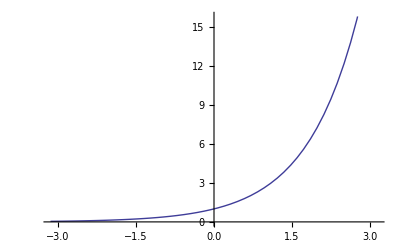

-1

Cosh[x]+Sinh[x]

-1

0

```mathematica
Plot[Exp[x],{x,-π,π}]
Exp[π*I]
ExpToTrig[Exp[x]]
Cosh[π*I]
Sinh[π*I]
```

(b) Plot ln(x) over the range {x, -2, 2}.  Then evaluate ln(1) and ln(-1).  While the second result may surprise you, recall that we have already demonstrated the inverse relation, ⅇ^(π i) = -1.

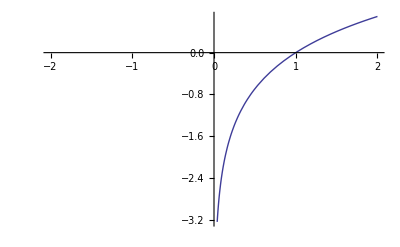

0

ⅈ π

```mathematica
Plot[Log[x],{x,-2,2}]
Log[1]
Log[-1]
```

(c) Almost any function defined over the real numbers can also operate in the complex plane.  In general, when we feed a function a complex argument of the form z = x + i y, we expect a complex result.  Use ComplexExpand to separate the real and imaginary parts of ⅇ^(x+i y).  From the results, you can see that a complex function can be viewed as two separate functions, a real one and an imaginary one.

```mathematica
ComplexExpand[Exp[x+I*y]]
```

ⅇ^x Cos[y]+ⅈ ⅇ^x Sin[y]

(d) Here, we use ComplexExpand to separate the real and imaginary parts of ln(x + i y).  We also perform some variable substitutions and simplifications in order to represent the result in terms of the magnitude and the phase of z = x + i y = r ⅇ^(i ϕ).  Evaluate the cell and use the resulting expression to explain why ln(-1) = π i .

```mathematica
Log[x+I y]//ComplexExpand
%/. {Arg[x+I y]->ϕ, x^2+y^2->r^2}//Simplify[#,r>0]&
```

ⅈ Arg[x+ⅈ y]+1/2 Log[x^2+y^2]

ⅈ ϕ+Log[r]

(e)  Evaluate cos(i z) and cosh(i z).  Any surprises?  Then use TrigToExp to obtain the exponential forms of cos(z) and cosh(z), which should help you to see the origin of these identities.

```mathematica
Cos[I*z]
Cosh[I*z]
TrigToExp[#]&/@{Cosh[I*z],Cos[I*z]}
```

Cosh[z]

Cos[z]

{ⅇ^(-ⅈ z)/2+ⅇ^(ⅈ z)/2,ⅇ^-z/2+ⅇ^z/2}

### (#7-#9) Calculus in the complex plane (25 min)

#### (#8) Power series expansions (5 min)

(a) Use D to compute the first derivative of e^(-z^2) with respect to complex variable z.  Observe that the result is the same whether or not you think of z as a complex.

```mathematica
D[Exp[-z^2],z]
```

-2 ⅇ^(-z^2) z

(b) Compute the 10^th-order power Series expansion of e^(-z^2) around the point z = 0 + 0 i .  Once again, observe that the result is the same whether or not you think of z as a complex.

```mathematica
Series[Exp[-z^2],{z,0,10}]
```

1-z^2+z^4/2-z^6/6+z^8/24-z^10/120+O[z]^11

(c) Compute the 10^th-order power series expansion of ln(z) around the point z = i .  This time, you should see a result that is explicity complex.

```mathematica
Series[Log[z],{z,I,10}]
```

(ⅈ π)/2-ⅈ (z-ⅈ)+1/2 (z-ⅈ)^2+1/3 ⅈ (z-ⅈ)^3-1/4 (z-ⅈ)^4-1/5 ⅈ (z-ⅈ)^5+1/6 (z-ⅈ)^6+1/7 ⅈ (z-ⅈ)^7-1/8 (z-ⅈ)^8-1/9 ⅈ (z-ⅈ)^9+1/10 (z-ⅈ)^10+O[z-ⅈ]^11

#### (#11) Radius of convergence (10 min)

(a) Evaluate the cell below to compute the 6^th-order series expansion of ⅇ^x around z = 0, and observe that the coefficient of the z^n term is a_n=1/(n!).

```mathematica
f = Exp[z]
ser = Series[f,{z,0,6}]
```

ⅇ^z

1+z+z^2/2+z^3/6+z^4/24+z^5/120+z^6/720+O[z]^7

(b) A series like ∑_(i=0)^∞ a_n z^n may not converge for all complex values of z.  In general, the series will only converge when |z| is less than some "radius of convergence".  Two techniques for determining the radius of convergence R are the Cauchy limit test, 1/R= lim _(n→∞) |(a_(n+1))/a_n|, and the Cauchy-Hadamard limit test, 1/R= lim _(n→∞) √(|a_n|).  Evaluate the cells below, where both tests agree on an infinite limit of convergence for the series expansion of ⅇ^z at z = 0.  This simply means that the series expansion converges for any value of z (as we might expect).

```mathematica
cauchytest:=Limit[Abs[cof[n+1]/cof[n]],n->Infinity]
cauchyhadamardtest := Limit[ Abs[cof[n]]^(1/n),n->Infinity]
```

```mathematica
cof[n_] := 1/n!
cauchytest
cauchyhadamardtest
```

General::ivar: 2.  + 0.05\ ⅈ
 is not a valid variable.

Limit[0.333287,2.+0.05 ⅈ→∞]

General::ivar: 2.  + 0.05\ ⅈ
 is not a valid variable.

Limit[0.707408+0.00612118 ⅈ,2.+0.05 ⅈ→∞]

(c) Consider the series,  ∑_(i=0)^∞ a_n z^n, where a_n=((n+3)/(2n+1))^n.  Evaluate the cell below to see that the radius of convergence is finite (R = 2).

```mathematica
cof[n_] := ((n+3)/(2n+1))^n 
1/cauchytest
1/cauchyhadamardtest
```

General::ivar: 2.  + 0.05\ ⅈ
 is not a valid variable.

1/Limit[0.629672,2.+0.05 ⅈ→∞]

General::ivar: 2.  + 0.05\ ⅈ
 is not a valid variable.

1/Limit[1.0001-2.49817×10^-6 ⅈ,2.+0.05 ⅈ→∞]

(d)  Here, we test the radius of converge (R = 2) by numerically evaluating the series  ∑_(i=0)^∞ ((n+3)/(2n+1))^n z^n for several different values of z.  Explain the output to your TA.

```mathematica
cof[n_] := ((n+3)/(2n+1))^n 
g[z_] :=NSum[cof[n]*z^n,{n,0,Infinity}]

g[I]
g[1+I]
g[3] (*outside raduis of convergence and therefore no [finite] solution *)
```

0.28004+0.861154 ⅈ

-0.26081+2.94373 ⅈ

ComplexInfinity

#### (#13) The residue theorem (10 min)

An important theorem of complex analysis states that when we integrate a function along a right-handed closed path in the complex plane (e.g. a circle), the result is equal to the 2πi  times the sum of the residues of any poles enclosed by the path.  This theorem turns out to be a powerful tool for solving really hard definite integrals.  The purpose of this exercise is to obtain the residues of a function by computing circular path integrals in the complex plane and to help you to visualize the whole concept.

(a) Evaluate the cells below.  The first cell defines g(z) = 3/( z+z^3), which has three poles in the complex plane (z = -i, z = 0, z = i ), and computes its Laurent series around the pole at z_0 = 0.  The second cell plots g(x) in the region of the complex plane containing the poles and also shows the integration path (defined parametrically) as a thick black circle.  The third cell prepares and executes the path integral.

(b) Now change z_0 and r and reevaluate the cells below in order to try the integration around each of the other two poles.  Make sure that the integration path encloses only one pole at a time.  Record (on a piece of paper) the residue of each pole.

(c)  Change z_0 back to 0 and make r large enough to include all three poles.  Verify that this larger path integral yields the sum of the enclosed residues.

```mathematica
Clear["`*"]
```

```mathematica
g[z_] := 3/(z+z^3)

z0 = I;  r= 1/2;  (* z0 is the expansion point, r is the integration-path radius *)

Series[g[z],{z,z0,6}]
```

-3/(2 (z-ⅈ))-(9 ⅈ)/4+(21 (z-ⅈ))/8+45/16 ⅈ (z-ⅈ)^2-93/32 (z-ⅈ)^3-189/64 ⅈ (z-ⅈ)^4+381/128 (z-ⅈ)^5+765/256 ⅈ (z-ⅈ)^6+O[z-ⅈ]^7

```mathematica
parametricpath[th_] := {r*Cos[th]+Re[z0],r*Sin[th]+Im[z0], Abs[g[r*(Cos[th]+I Sin[th])+z0]]}

Show[
Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black},PlotRange->All]
]
```

-Graphics3D-

```mathematica
z0 =- I;  r= 1/2;
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ] /(2 Pi I)
residue = Integrate[integrand ,{θ,0,2Pi}] (*This is for Z = -I*)
```

(3 ⅇ^(ⅈ θ))/(4 (-ⅈ+ⅇ^(ⅈ θ)/2+(-ⅈ+ⅇ^(ⅈ θ)/2)^3) π)

-3/2

```mathematica
z0 = I;  r= 1/2;
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ] /(2 Pi I)
residue = Integrate[integrand ,{θ,0,2Pi}] (*This is for z = I *)
```

(3 ⅇ^(ⅈ θ))/(4 (ⅈ+ⅇ^(ⅈ θ)/2+(ⅈ+ⅇ^(ⅈ θ)/2)^3) π)

-3/2

```mathematica
z0 = 0;  r= 1/2;
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ] /(2 Pi I)
residue = Integrate[integrand ,{θ,0,2Pi}] (*This is for z=0*)
```

(3 ⅇ^(ⅈ θ))/(4 (ⅇ^(ⅈ θ)/2+1/8 ⅇ^(3 ⅈ θ)) π)

3

```mathematica
z0 = 0;  r= 3/2;
zzz= z0 +  r*Exp[I θ];
integrand = g[zzz] D[zzz,θ] /(2 Pi I)
residue = Integrate[integrand ,{θ,0,2Pi}] (*This is for z=0 with larger r to include all three points, residual =0 so good!*)
```

(9 ⅇ^(ⅈ θ))/(4 ((3 ⅇ^(ⅈ θ))/2+27/8 ⅇ^(3 ⅈ θ)) π)

0

## Applications (45 min)

### (#10) Light absorption (10 min)

Because light is an electromagnetic wave, we can describe it in terms of electric and magnetic fields that propagate as travelling waves.   The electric-field of a linearly-polarized laser beam travelling along the x direction, for example, can be described by complex sinusoid, A ⅇ^(i (k x - ω t)), where A is amplitude, k is wavevector and ω is angular frequency.  The position dependence of the electric field at time t = 0 (i.e. a snapshot) can then be written as A ⅇ^(i k x).

All materials absorb light.  Highly transparent material absorb only weakly, while other material absorb strongly and therefore appear to be opaque.  The phenomenon of absorption is best described in terms of a complex electric permitivity (ϵ) which then leads to a complex index of refraction (n = √(ϵ/ϵ_0)) and a complex wavevector (k = n ω /c).

(a)  In the cell below, express the electric field as ⅇ^(i k x) (implying that the incident amplitude is A = 1).  Next, use variable replacement to make the wavevector explicitly complex (i.e. k → k_R + i k_I).  Then demonstrate that Re and ComplexExpand work together to produce an expression for the real part of the field that doesn't contain i.   Finally, explain to your TA the distinct roles that k_R and k_I play in the x-dependence of the field.

```mathematica
Clear["`*"]
```

```mathematica
field[x_]:=  Exp[I*k*x]
```

```mathematica
kf[x_]:=field[x]/.k->{(kr+I*ki)}
ComplexExpand[Re[kf]]
```

kf

(b) An optical material with complex index of refraction n = 2 + 0.05i  for red light (ω ~ 3×10^15rad/sec) for example will have wave-vector k_R+k_I = 20 + 0.5i  μm^-1.  Make this replacement (e.g. k_R → 20 and k_I → 0.5) and plot the electric field as a function of x over the range from 0 to 10 μm.

20.+0.5 ⅈ

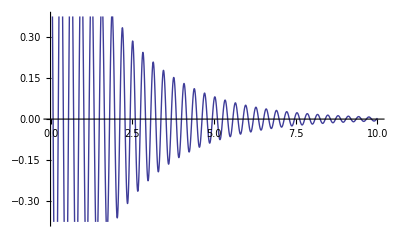

```mathematica
n= 2+0.05*I;
wred=3*^15;
k = 20+0.5*I
plotfield[x_]:=kf[x]/.{kr->20,ki->0.5}
Plot[ComplexExpand[Re[plotfield[x]]],{x,0,10}]
```

### (#11) Electrostatics (15 min)

An analytical technique known as the "conformal mapping" makes it possible to use the complex plane to visualize 2D electric-field distributions.  Suppose that we have an infinite line charge with charge density λ running perpendicular to the xy plane.  The field in the plane will then be equal to - (λ ln(r))/(2 π ϵ_0), where r = √(x^2+y^2)is perpendicular distance from the line charge.  Now, if we replace the distance r in this expression with complex number z = x + i y , something fascinating happens -- the real part turns out to be the electric potential in the plane, and readily yields equipotential contour lines.  And if this isn't weird enough already, the contours of the imaginary part are the electric field lines.

(a) Evaluate the cell below, where we Plot3D the real part of g(z) = -ln(z) and use MeshFunctions to draw in lines of constant Re(z) and Im(z).  Observe that the real part corresponds to the electric potential of a point charge, while the imaginary part produces the corresponding field lines.

```mathematica
g[z_] := -Log[z]
Plot3D[Re[g[x+I y]],{x,-3,3},{y,-3,3},MeshFunctions->{Re[g[#1+I #2]]&,Im[g[#1+I #2]]&},MeshStyle->{{Thick,Orange},{Thick,Green}}]
```

-Graphics3D-

(b) Copy the code from the previous cell into the cell below.  Then evaluate the cell for each of the following functions g(z).  Modify the same line each time -- don't make multiple copies of the same code.
	(1) Two line charges of opposite signs:  ln(z-1) - ln(z+1)
	(2) Two line charges of the same sign:    -ln(z-1) - ln(z+1)
	(3) The edge of a sharp sheet of charge:  √z

```mathematica
Manipulate[Plot3D[Re[func[x+I y]],{x,-3,3},{y,-3,3},MeshFunctions->{Re[func[#1+I #2]]&,Im[func[#1+I #2]]&},MeshStyle->{{Thick,Orange},{Thick,Green}}],{func,{-Log[#]&,-Log[#+1]+Log[#-1]&,-Log[#-1]-Log[#+1]&,√#&},ControlType->Setter,ControlPlacement->Bottom}]
```

### (#12) Steady-state circuit analysis (20 min)

In a previous lab exercise, we explored both transient and steady-state effects in a damped mechanical oscillator system.  Here, we will explore the time-independent amplitude of a steady-state oscillation to gain experience working with complex sinusoids of the form ⅇ^(i ϕ).

(a) A series electrical circuit containing an inductor (L), a resistor (R) and a capacitor (C) is another example of a damped harmonic oscillator.  The relevant differential equation is L(d^2 q)/(d t^2)+R (d q)/(d t)+q/C=V ⅇ^(i ω t), where q(t) is the charge on the capacitor, and v(t) = V ⅇ^(i ω t) is a sinusoidal driving voltage with amplitude V.  Knowing that the steady-state solution to this equation is sinusoidal, we simply define a trial solution of the form q(t) = Q ⅇ^(i (ω t+ϕ)) that contains an unknown amplitude (Q) and phase (ϕ).  Substituting the trial solution into the differential equation produces an ordinary complex equation containing both Q and ϕ.  Also knowing that these steady-state parameters can't depend on time, we use variable replacement to set t → 0.  We call the result steadyq.

```mathematica
diffeq =L q''[t] + q[t]/c + R  q'[t]- V Exp[I w*t]==0
trial[t_] := Q*Exp[I(w*t+phi)]
steadyq = diffeq/.q->trial /. t->0
```

-ⅇ^(ⅈ t w) V+q[t]/c+R q'[t]+L q''[t]==0

(ⅇ^(ⅈ phi) Q)/c-V+ⅈ ⅇ^(ⅈ phi) Q R w-ⅇ^(ⅈ phi) L Q w^2==0

(b)  A complex equation is really two separate equations, a real one and an imaginary one.  Use Re and Im to separate these two equations, ComplexExpand them, which conveniently forces the assumption that all of the variables are real, and give them both names.  Note that because Re and Im only know how to swallow simple expressions (not equations), you must map (/@) them onto an equation in order to hit both sides.

```mathematica
real=ComplexExpand[Re/@steadyq]
imaginary=ComplexExpand[Im/@steadyq]
```

-V+(Q Cos[phi])/c-L Q w^2 Cos[phi]-Q R w Sin[phi]==0

Q R w Cos[phi]+(Q Sin[phi])/c-L Q w^2 Sin[phi]==0

(c)  Solve your pair of equations for the unknown amplitude (Q) and the unknown phase (ϕ) and Simplify the result.  Then use variable replacement to isolate a physically meaningful expression for Q.  Now that we know the charge amplitude Q, it's a trivial matter to obtain the current amplitude, which is computed as |(d q)/(d t)| = |d/(d t)(Q ⅇ^(i (ω t+ϕ)))| = |i ω Q ⅇ^(i (ω t+ϕ))| = ω Q.  So multiply your expression for Q by the driving frequency (i.e. w) and call the result currentamp.

```mathematica
Clear[Q,currentamp]
```

```mathematica
currentamp = w*( Q/.Simplify[Solve[{real,imaginary},{Q,phi}]][[4,1]])
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(c V w)/(√(1-2 c L w^2+c^2 w^2 (R^2+L^2 w^2)))

(d)  Evaluate currentamp for the special case when {R → 1, L → 1, V → 1, C → 1} and Simplify it to obtain a clean expression containing only the driving frequency.  Then LogLinearPlot this expression over the range {w, 0.01, 100}.  Think carefully about what the horizontal and vertical axes represent, and explain the physical meaning of the graph to your TA.

w/(√(1-w^2+w^4))

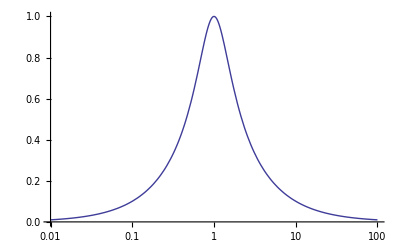

```mathematica
temp = currentamp/.{R -> 1, L -> 1, V -> 1, c -> 1}//Simplify
LogLinearPlot[temp,{w,0.01,100}]
```

(e)  Redraw the current-amplitude graph above for the special case when {R → 1, L → 0, V → 1, C → 1}.  Removing the inductor from the circuit produces a "high-pass filter".  Can you see the reason for this name?

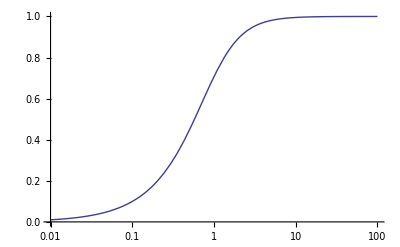

```mathematica
LogLinearPlot[currentamp/.{R -> 1, L -> 0, V -> 1, c -> 1},{w,0.01,100}]
```

(f)  (Optional) Redo the current-amplitude graph for the special case when {R → 1, L → 1, V → 1, C → Infinity}.  Note that you might need to employ a Limit to handle the capacitor.  Removing the capacitor from the circuit produces a "low-pass filter".  Can you see the reason for this name?

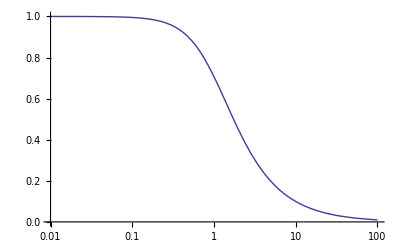

```mathematica
LogLinearPlot[Limit[currentamp/.{R -> 1, L -> 1, V -> 1, c -> clim},clim->Infinity],{w,0.01,100}]
```

## On Your Own (45 min)

```mathematica
Clear["`*"]
```

### (#13) Fresnel Coefficients (10 min)

The equations for reflection and transmission of light from an interface are given in the Wikipedia article at http://en.wikipedia.org/wiki/Fresnel_equations.  For light going from vacuum (n1=1) to a medium with a complex index of refraction n2=0.9-0.05 ⅈ, plot the reflection coefficients for s and p polarization on a semilog plot.  In the extreme ultraviolet and x-ray regions where such indices of refraction are most common, it is conventional to measure the angle as degrees from grazing incidence rather than normal incidence as in the Wikipedia article.  Please use that convention here as well.

```mathematica
th2=θ2[θ1,n1,n2];
θ2[θ1_,n1_,n2_]:= ArcSin[n1/n2*Sin[θ1]]
```

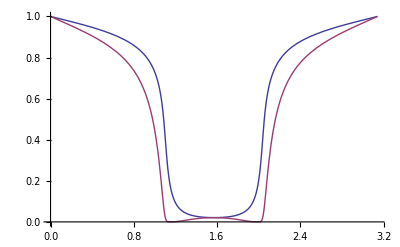

```mathematica
n1=2;
n2=0.9-0.05*I;
rs[θ1_,n1_,n2_]:=Module[{th1=π/2-θ1},
((n1*Cos[th1]-n2*√(1-((n1/n2)*Sin[th1])^2))/(n1*Cos[th1]+n2*√(1-(n1/n2*Sin[th1])^2)))^2
]
rp[θ1_,n1_,n2_]:=Module[{th1=π/2-θ1},
((n1*√(1-((n1/n2)*Sin[th1])^2)-n2*Cos[th1])/(n1*√(1-((n1/n2)*Sin[th1])^2)+n2*Cos[th1]))^2
]
Plot[{Abs[rs[x,n1,n2]]^2,Abs[rp[x,n1,n2]]^2},{x,0,π},GridLines->{{{π/2,Red}},{}}]
```

The place where the reflection of p-polarized light is at a minimum is known as Brewster’s angle.

### (#14) Quantum Time Evolution (20 min)

A quantum mechanical particle in a rigid one-dimensional box of width a has a wave function ψ_n(x,t)=(sin((π n x)/a) exp((ⅈ e_n t)/ℏ))/(√a), where x=0 on one side of the box and x=a on the other side.  The variable n is a positive integer.  The energy of these states is given by e_n=(π^2 n^2 ℏ^2)/(2 a^2 m).  The probability of finding a particle at the position x at time t is given by P(x,t)=Abs[ψ_n(x,t)]^2.  States with a definite energy, have probabilities that don’t depend on time.  However, it’s possible to have states that are a combination of states with definite energies.  These states have probabilities that oscillate in time.

Create a state ψ(x,t)=a_3 ψ(x,t)+a_1 ψ_1(x,t)+a_2 ψ_2(x,t), with a_1=0.3+ⅈ/3, a_2=-0.4-ⅈ/7 and a_3=10.135575+0.357482 ⅈ.  Create an animated plot of P(x,t)=Abs[ψ(x,t)]^2 for times from 0 to 10 femtoseconds.  Use a=1 nm, ℏc=197 eV-nm, m=(511000 eV)/c^2, hbar = 0.656667 ev-fs.  Your work will come out nicest if you keep energies in eV (electron Volts) and times in fs (femtoseconds).

```mathematica
Clear["`*"]
```

```mathematica
a1 = 0.3+I/3;
a2 = -0.4-I/7;
a3 = 10.135575+0.357482*I;
m = 5.11*^6/(3*^8);
hbar= .656667;
a=1;
```

```mathematica
ψ[x_,t_,n_]:=(Sin[(π*n*x)/a]*Exp[(I*e[n]*t)/hbar])/(√a)
e[n_]:=(π^2*n^2*hbar^2)/(2*a^2*m)
```

```mathematica
plotψ [x_,t_]:= ψ[x,t,1]*a1+ψ[x,t,2]*a2+ψ[x,t,0]*a3;

Manipulate[Plot[Abs[plotψ[x,t]]^2,{x,-5,5},PlotRange->{0,1}],{t,0,10,0.1}]
```

### (#15) Complex Impedance (15 min)

Find the equivalent impedance of a complicated network.

A circuit with resistors, capacitors, and inductors driven at a single frequency ω can be represented as a complex voltage V=ⅇ^-Iωt V_0 acting on individual elements with complex impedances Z.  Each element then obeys the complex form of Ohm’s Law with the current I =I_0 E^(I ω t)  proportional to the voltage V according to V=I Z.

For a resistor with resistance R, the real form of Ohm’s Law holds and Z=R since V=I R.

For a capacitor, the charge Q is equal to the capacitance C V.  Since I=dQ/dt, Q=∫Iⅆt=-I/(ⅈ ω).  This means that -I/(ⅈ ω)=C V and that V=I {1/(ⅈ C ω)}.  Thus, Z=ⅈ/(C ω).

For an inductor, V=L dI/dt.  With the assumed time dependence of I, V=-ⅈ L ω I and Z is thus -ⅈ L ω.

Using these complex substitutions, an AC circuit can now be solved algebraically rather than requiring the use of differenatial equations.  Consider the 3rd order Butterworth filter below we found diagrammed on Wikipedia.  It can be used as a low-pass filter which allows low frequency voltages to pass from V_in to V_out but attenuates higher frequencies.
 
-Graphics-

You can solve for V_out by applying Kirkhoff’s Laws at the junction J in the middle of the top of the circuit and around the left and right loops.  Kirkhoff’s First Law comes from conservation of charge.  If charge is to be conserved, the total current in and out of the junction J just be zero.  Letting I_1 , I_2, and  I_3 being the currents through L_1, C_2, and L_3 (and R_4) as shown, this requires that I_1=I_2+I_3.  

-Graphics-

Kirkhoff’s Second Law is related to conservation of energy.  It implies that the voltage change around any closed loop be zero.   Thus, for the left loop we have V-I_1 Z_1-I_2 Z_2=0.  For the right loop we have Z_2 I_2-Z_3 I_3-Z_4 I_3=0.

These laws give us three complex equations for the three unknown currents I_1 , I_2, and I_3.  The current I_3  is the current through the resistor R_4 as well as through L_3.  Therefore the voltage V_out  must equal I_3 R_4.  

Let L1=3/2 H, C2=1/7500 F, L3=1/2 F, and R4=100 Ω.  Solve the coupled complex equations resulting from applying Kirkhoff’s Laws.  Letting V_in=1 Volt, plot the magnitude and phase of voltage V_out as a function of the frequency ω for ω from 0 to 300 radians per second.  What is the frequency at which the filter cuts off?

```mathematica
Clear["`*"]
```

```mathematica
l1 = 3/2; c2 = 1/7500; l3 = 1/2; r4 = 100; vin = 1;
z1 = -I*l1*w;
z2 = I/(c2*w);
z3 = -I*l3*w;
z4 = r4;
{eq1,eq2,eq3} = {
i1== i2+i3,
vin-i1*z1-i2*z2== 0,
i2*z2-i3*z3-z4*i3== 0
}
Solve[eq1&&eq2&&eq3,{i1,i2,i3}][[1]]
```

{i1==i2+i3,1-(7500 ⅈ i2)/w+(3 ⅈ i1 w)/2==0,-100 i3+(7500 ⅈ i2)/w+(ⅈ i3 w)/2==0}

{i1→-(2 (15000 ⅈ+200 w-ⅈ w^2))/(3 (-1000000 ⅈ-20000 w+200 ⅈ w^2+w^3)),i2→(2 ⅈ (200 ⅈ w+w^2))/(3 (-1000000 ⅈ-20000 w+200 ⅈ w^2+w^3)),i3→-(10000 ⅈ)/(-1000000 ⅈ-20000 w+200 ⅈ w^2+w^3)}

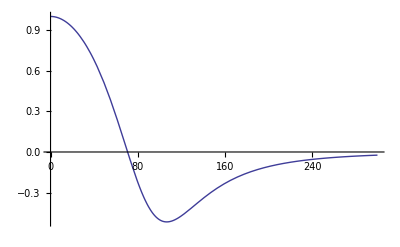

```mathematica
Plot[Re[-(10000 ⅈ)/(-1000000 ⅈ-20000 w+200 ⅈ w^2+w^3) * 100],{w,0,300}]
```

```mathematica
Z=ⅈ/(C ω) (*capacitor*)
Z =  -ⅈ L ω (*inductor*)
Z=R (*resistor*)
```